```mathematica
AutoCollapse[]:=(If[$FrontEnd=!=$Failed,SelectionMove[EvaluationNotebook[],All,GeneratedCell];
FrontEndTokenExecute["SelectionCloseUnselectedCells"]]);
HideText[x_]:=(Print[x];AutoCollapse[]);
HideText["Clear Data..."];
```

Clear Data...

```mathematica
<<MaTeX`
SetOptions[MaTeX,"Preamble"->{"\\usepackage{physics,nicefrac,esint,siunitx,bm}"},"Magnification"->1.5];

MyTeX[x_]:=HideText[MaTeX[x]];
HideText["Load MaTeX..."]
```

Load MaTeX...

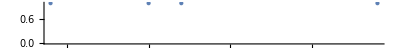

```mathematica
data={{"1","1'","2'","3'"},{.267,.261,.257,.260}};
lineplot=NumberLinePlot[data[[2]]]
```

```mathematica
5
```

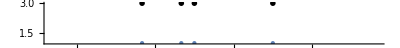

```mathematica
lineplotLabeled=Show[{lineplot,
Table[Graphics[Text[MaTeX[data[[1,i]],Magnification->1.2],{data[[2,i]],3}]],{i,4}]
},PlotRange->{{.25,.275},All}]
SetDirectory@NotebookDirectory[];
Export["lineplot.pdf",lineplotLabeled];
```